Last modified on: Tuesday, July 10, 2018 at 22:56

Author Info

Aghil Abed Zadeh

Markus van Almsick

Duke University

Poster Session Content

A Discourse Language for Card Games

This project aims at constructing a platform to define any card game for Mathematica and further process, play and analyze the game.

Add the most representative image of your project here. (We recommend just 1 image, if you add more, we will make a collage of the images.)

-Graphics-

We have implemented a simple structure to introduce game state, perform actions on the game state based on defined rules, play and visualize the game automatically, and construct the game tree of possible moves. The definition of a game has four main parts: game state, actions, rules, and goals. 
By constructing an initial game state and selecting a list of rules, a game can be visualized and played randomly or the game tree can be constructed. Furthermore, there exist tools to analyze the game statistically.

The project can be generalized to a broader class of games and can be used to train a neural net for finding game strategies.

Note: Everything above this bar is your poster.Make sure it fits on a single page. "Preview Poster"

End of School Presentation Content

In addition to the poster content, include other content to present at the 2 minute presentation for end of school. Use the buttons below to add more sections."Add Header""Add Text""Add Code or Image"

PLATFORM STRUCTURE

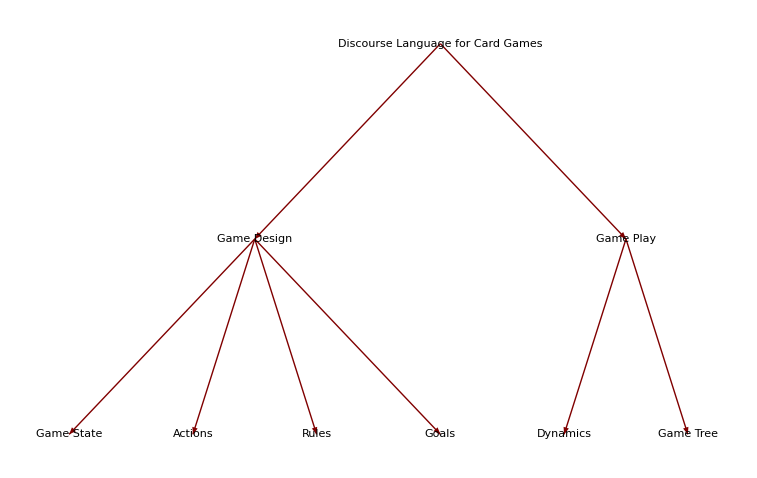

GAME PLAY

rules = {rule1, rule2, rule3};
PlayGameList[initialState, rules, maxsteps]
-Graphics-

STATISTICS

initialStateList = Table[CreateGameState[playersList, handsN], 100];
WinnersList = WinnerofRandomPlay[#, rules]& /@ initialStateList;
-Graphics-

GAME TREE

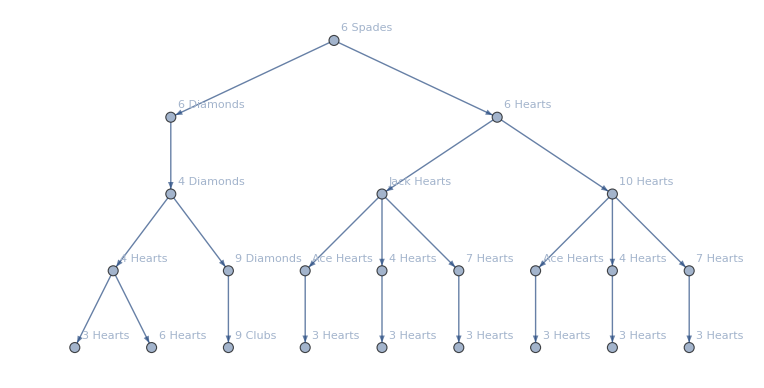
graph = GameTree[initialState, rules, 4];
PlotGameTree[graph]
-Graphics-

Note: Everything above this bar is in your 2 minute presentation. Make sure it fits on 2 slides. "Preview Presentation"

Detailed Project Notes

#### Main Results in Detail

We introduce a discourse language to define and play card games. 

In our data structure, there are four main parts of game design: game state, action, rule, and goal
Game state is an association with all needed information in one step of the game. It consists of players and other hands related to a list of cards, and also a control state, showing who controls the game at that step.
Actions are functions that map a game state to another.
Rules have a “rule delayed” structure (lhs /; conditions :> rhs),  in which the lhs is an association pattern, conditions are the game rules, and rhs is an action. This structure can easily reproduce next step using Replace function.
Goal part computes the score and checks the end of the game.

The next part of the code is game play, in which functions for different kind of the game are represented. Also the game tree can be computed and visualized by functions in this section.

Last part shows how to play a simple game, named Crazy Eight. In this game each player at his turn should drop a card on stock with the same suit or same number as stock top. Otherwise, the player  draws a card from stack and the game goes to the next player. We can play it randomly and

#### Code

Link to the GitHub: https://github.com/AghilZadeh/Summer2018Starter/blob/master/StudentDeliverables/A%20Discourse%20Language%20for%20Card%20Games.nb

#### Conclusions in Detail

#### Future Directions

There are several other functions that can be implemented in the game. One of them is See function that outputs the information that each player has at any game state. With this add-on, and also designing a reward or score function, the game can be trained to a neural net and a computer game player can be developed. 
Also, a more general game implementation can be followed using the same method.

#### Background Info Links/References

http://logic.stanford.edu/classes/cs227/2013/readings/gdl_spec.pdf

#### Keywords

Provide keywords as items

card game

game theory

game description language